## Plot Examples-2 Scatter Graphs

Scatter graphs are data collected pointwise. They can be collected by direct observations or from mathematical relations including randomly generated data.

We will begin by sequential data. These data come one by one, that is one point after a previous one. Suppose you measure the viscosity of a mixture every after rise of two degrees beginning from an inital of 18 °C . The observed viscosity value is measured after the exact temperature equilibrium of the mixture and heating medium and it is known that the viscosity is stable infinitesimally at a given constant temperature. The collected data will be as,

Temperature (°C) | Nr. of Observation (n) | Observed value of the viscosity.
15 (initial) | 1 | 2.16
17 | 2 | 3.86
19 | 3 | 5.23
21 | 4 | 6.11
23 | 5 | 7.82
25 | 6 | 9.28
27 | 7 | 13.88
29 | 8 | 23.77
31 | 9 | 28.18

Since, number of observation is a direct informant of the equilibrium temperature, we can satisfy with only two values,

Number of observation,

Observed value of the viscosity.

Nr. of Observation | Observed value of the viscosity.
1 | 2.16
2 | 3.86
3 | 5.23
4 | 6.11
5 | 7.82
6 | 9.28
7 | 13.88
8 | 23.77
9 | 28.18

If we wish to plot Nr of Observation versus observed value, we do not need to provide a {temperature, observed value of the viscosity} data doublet. A data doublet {nr. of observation , observed value of the viscosity}  may suffice.  Number of observation will be the abcissa of the point (x) and the observed value of the viscosity will be the ordinate value.(y).

We ought to provide only a one dimensional sequential data list (a simple Mathematica list), the number of observation will be automatically generated by Mathematica as the ordinal numbers of the entered data. In computer science it is called the “index” of the the elements of a given list. In Mathematica list indexes are beginning by 1 and increasing by 1 up to the end of the entered data. One may access the the elements of a defined list referring the index value of a given element.

```mathematica
data = {2.16,3.86,5.23,6.11,7.82,9.28,13.88,23.77,28.18};
```

This list, Now we can plot this sequential data,

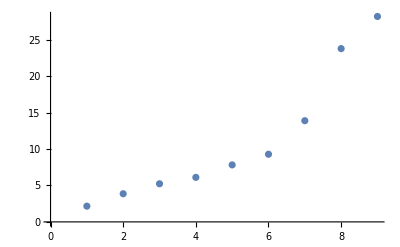

```mathematica
p1=ListPlot[data]
```

In obtained plot, abcissa values were assigned in situ, according to the order of the entered data in the list named (data). The first of these values (elements of the list) which may also be interpreted as a vector ( the computer name for the one dimensional sequential data) or a set is the observed value of the viscosities at the experiment

The observed value of the viscosity in the initial temperature is,

```mathematica
data[[1]]
```

2.16

The 9 th. observation is,

```mathematica
data[[9]]
```

28.18

We have regular increase in temperature during the experiment, that means we can develop a relation calculating the temperatures for each entry of viscosity data to experiment list.

The first entry is the viscosity at the initial temperature 15 (°C)

Let us assign n for the index of the viscosity value.

For the first entry point n = 1 and t = 15 (°C) = 15 + n-1 = 15 (°C)  or 15 + 2 (n-1) = 15 + 1 (1-1) = 15 + 0 = 15 (°C)

For the second entry point n = 2 and t = 15 + 2 (°C) = 15 + 2 (n-1) = 15 + 2 (2-1) = 15 + 2 = 17 (°C)

.....

For the ninth entry point n = 9 and t = 15 + 2 (n-1) = 15 + 2 (9-1) = 15 + 2×8 = 15 + 16 = 31 (°C)

Since the initial temperature and the temrature step are constants, we can define a more general relation valid for either different initial temperatues and the temperature increase steps.

```mathematica
initialTemp = 15; tempStep= 2;
```

We can devise a user defined function for this entry point / temperature relation. The variable n will be defined as the index (ordinal number) of the data set.

```mathematica
F[n_] = initialTemp + tempStep(n-1)
```

15+2 (-1+n)

We can determine the temperatures for each determined value of viscosity in our experiment.

list = Table[iteratedValue , {iterator, initial value of the iterator , end value of the iterator , (increase / decrease) value of the iterator}]

```mathematica
temperature =Table[x, {x,initialTemp,F[Length[data]],tempStep}]
```

{15,17,19,21,23,25,27,29,31}

Now, we are in position to be able to plot the temperature of each entry point :

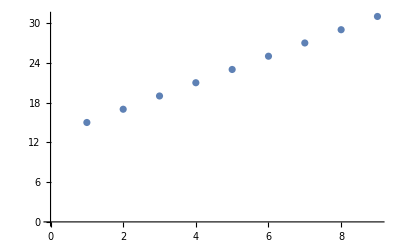

```mathematica
p2=ListPlot[temperature]
```

Temperaature is changing step by step from the initial to the final stage of the experiment. We call this “The Viscosity Chart of a Given Substance by Discrete Steps of Temperature”.

Observed viscosity values are stored in the list “data” and plotted above as p1. The temperature values of these experiment is stored in the list “temperature” and plotted above as p2. We can plot them side by side or in one single plot.

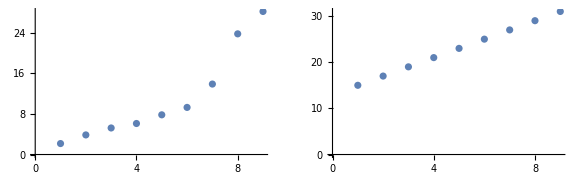

```mathematica
GraphicsRow[{p1,p2},ImageSize->Large]
```

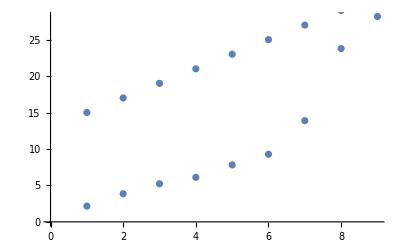

```mathematica
Show[p1,p2]
```

Surely a more conveniant plot may be a (temperature / viscosity) plot. This can be obtained by providing dual data coordinates for each point  (x , y) . The first of these values will be the abcissa value (x) and the second will be the ordinate value (y).

Before going any farther, we should discuss about the constitution of the list “temperature”. The elements of temperature list are calculated using the special deterministic user defined relation of the temperature values for each experiment step. This is more or less an unusual case. Most usual cases is recording viscosity values at different, unpredictable but constant experimental temperature values.

For each experiment, there is two possibilities of providing records for the evalution with Mathematica. The first of the possibilities is to devise two lists “temperature” and “viscosity” for each experiment. The other way is entering each data doublet as sublists in each experiment. Both ways are possible and feasible in Mathematica.

We will begin by providing two different lists for each experiment. The first list will be list named “temperature” and bear the experiment temperatures for each experiment set. The other list may be named as “data” and and his elements will be observed viscosity values for a given temperature. The list may or may not have any special ordering and may be entered freely one after another. The only requirement is to enter corresponding experimental data in the same order in two lists. That is, entry one should be some temperature of the experiment step in one list and the observed viscosity value at same temperature in the other list. Same should be the entry two and its successors. The number of the elements (Size) of the two sets will be same, since there is only one entry of temperature, corresponding a distinct reading of viscosity. This is the system which we have applied in entering the elements of ``temperature” and ``data” lists in our example.

When we have two lists for any experiment set, as “temperature” and “data”, in our example, we have two ways for assembling these two lists into one single list for a given experiment set in Mathematica.

We can make data doublets with Mathematica, by applying Matrix transposition :

```mathematica
data1 = {temperature,data}ᵀ
```

{{15,2.16},{17,3.86},{19,5.23},{21,6.11},{23,7.82},{25,9.28},{27,13.88},{29,23.77},{31,28.18}}

The other way is using Mathematica’s Table [ ] function. This may be achieved as :

```mathematica
data2 = Table[{temperature[[x]],data[[x]]},{x,1,Length[data]}]
```

{{15,2.16},{17,3.86},{19,5.23},{21,6.11},{23,7.82},{25,9.28},{27,13.88},{29,23.77},{31,28.18}}

That is it! We have obtained a data set consisting temperature/ viscosity data ready to be plotted.

Generally the common way of providing a temperature / viscosity data,  is to enter {temperatue, viscosity} data by hand as a sublists of the experience list :

```mathematica
data3= {{15,2.16},{17,3.86},{19,5.23},{21,6.11},{23,7.82},{25,9.28},{27,13.88},{29,23.77},{31,28.18}};
```

According the explanations above, these three lists are the same and consist the unique “experienceSet” :

```mathematica
data1 == data2 == data3
```

True

The combined list will be named as experienceSet for given experiment. The experience set will be unique, regardless of his elements are entered by hand, found by calculation or assembled from two independent sets.

```mathematica
experienceSet= data1;
```

We can plot either data1 , data2 , data3 or experienceSet, the result will be the same :

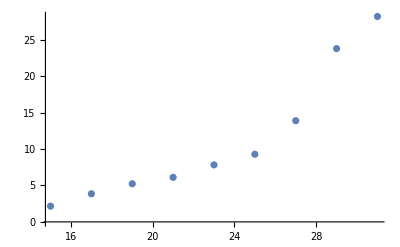

```mathematica
ListPlot[experienceSet]
```

This is more informative as a graph of the experimentation of course, but also it is a very primitive plot that should be enhanced for attaining a publishable quality.

First we will enclose the graph in a frame. This is nearly compulsory for producing quality graphs with Mathematica.

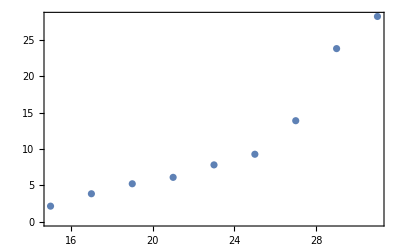

```mathematica
ListPlot[
experienceSet ,
Frame->True
]
```

Then we will decide for a size of plot. This can be achived with dragging from the edges with  the mouse. But ImageSize option is also works fine.

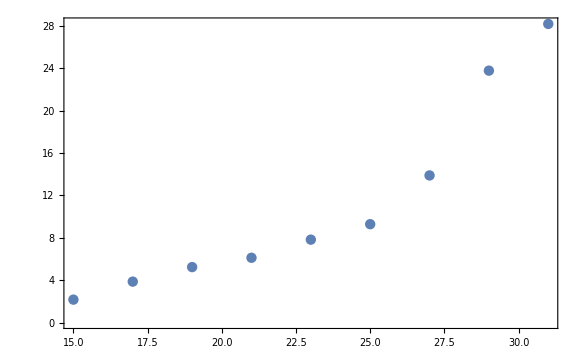

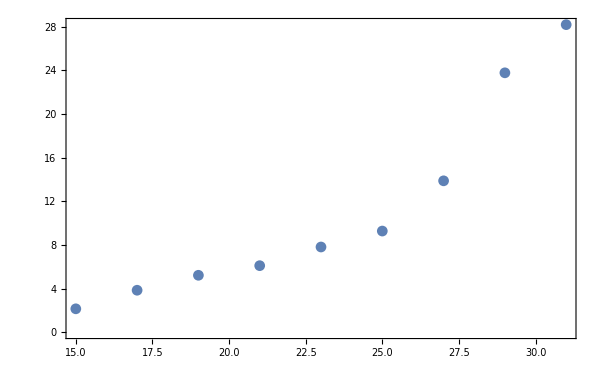

```mathematica
ListPlot[experienceSet ,
Frame->True,
ImageSize->600
]
```

We will give a name for the plot with PlotLabel rule of Mathematica :

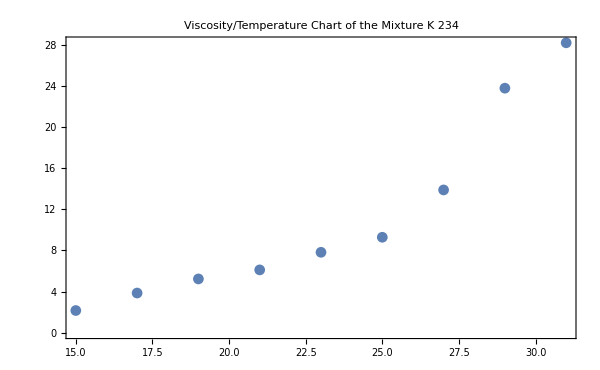

```mathematica
ListPlot[experienceSet ,
Frame->True,
ImageSize->600,
PlotLabel->"Viscosity/Temperature Chart of the Mixture K 234\n"
]
```

Open Mathematica Documents and search the options for the PlotLabel rule, That may be done by Style [ ] function of the Mathematica

```mathematica
ListPlot[experienceSet ,
Frame->True,
ImageSize->600,
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"]
]
```

-Graphics-

About PointSize,
PointSize is an important option for setting a point size relevant to the size of the graph.

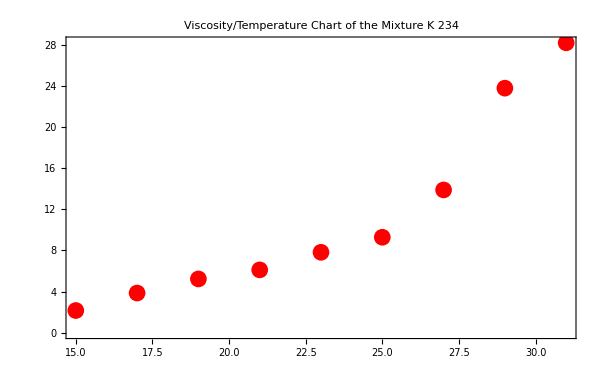

```mathematica
ListPlot[experienceSet ,
Frame->True,
ImageSize->600,
PlotStyle->{Red,PointSize[0.02]},
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"]
]
```

We can change plot markers :

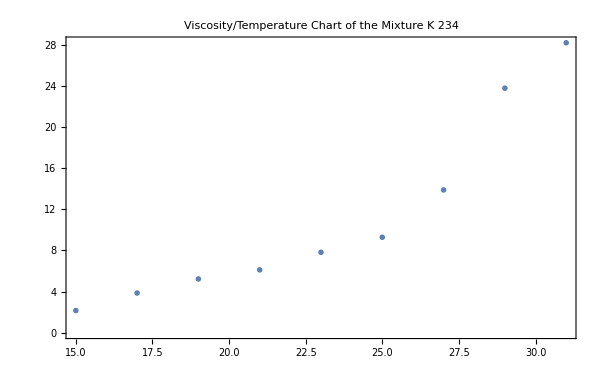

```mathematica
ListPlot[experienceSet ,
Frame->True,
ImageSize->600,
PlotStyle->Directive[PointSize[20]],
PlotMarkers->Style["x",Red, FontFamily-> "Segoe UI", FontSize->22],
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"]
]
```

Now we’ll define the frame for our taste, (Frame blue at x and orange at y axis, no frame at right and top)

```mathematica
ListPlot[experienceSet ,
Frame-> {{True,None},{True, None}},
FrameStyle->{{Directive[Thick,Orange],None},{{Thick,Blue},{None}}},
ImageSize->600,
PlotStyle->{Red,PointSize[0.02]},
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"]
]
```

-Graphics-

Frame Labels “Temperature” , “Viscosity”

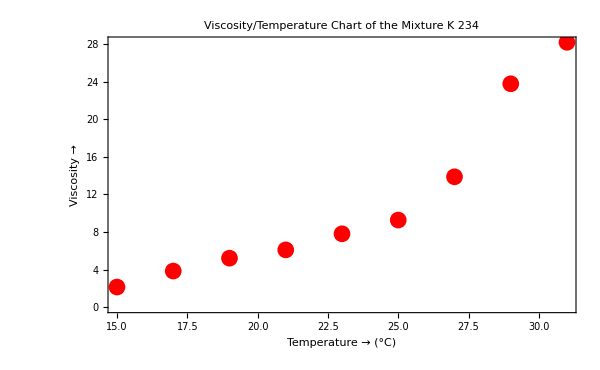

```mathematica
ListPlot[experienceSet ,
Frame-> {{True,None},{True, None}},
FrameStyle->{{Directive[Thick,Orange],None},{{Thick,Blue},None}},
FrameLabel->{{Style["Viscosity → \n",Orange, FontFamily-> "Segoe UI", FontSize->22],None},{Style["\nTemperature →  (°C) ",Blue, FontFamily-> "Segoe UI", FontSize->22],None}},
ImageSize->600,
PlotStyle->{Red,PointSize[0.02]},
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"]
]
```

We may arrange the ticks of the axes, (for framed plots the the axes are the sides of the frame).

Frame tics are defined via FrameTicks rule. This rule is applied using lists. General definition is,

FrameTicks → {{Left Side, Bottom} , {Right Side , Top}}

Generally we only need two lists one for left and right (if it exists), one for bottom and top (if it exists).

```mathematica
yList ={0,5,10,15,20,25,30};
```

```mathematica
xList = {15,17,19,21,23,25,27,29,31};
```

```mathematica
experienceSet
```

{{15,2.16},{17,3.86},{19,5.23},{21,6.11},{23,7.82},{25,9.28},{27,13.88},{29,23.77},{31,28.18}}

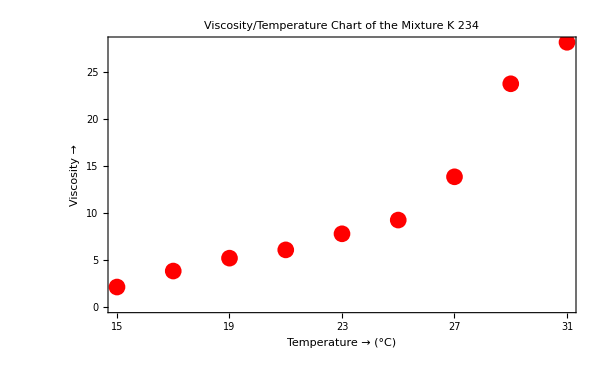

```mathematica
ListPlot[experienceSet ,
Frame-> {{True,None},{True, None}},
FrameStyle->{{Directive[Thick,Orange],None},{{Thick,Blue},None}},
FrameLabel->{{Style["Viscosity → \n",Orange, FontFamily-> "Segoe UI", FontSize->22],None},{Style["\nTemperature →  (°C) ",Blue, FontFamily-> "Segoe UI", FontSize->22],None}},
ImageSize->600,
PlotStyle->{Red,PointSize[0.02]},
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"],
FrameTicks->{{{0,5,10,15,20,25,30,35},None},{{15,17,19,21,23,25,27,29,31,33},None}}
]
```

Now grid lines,

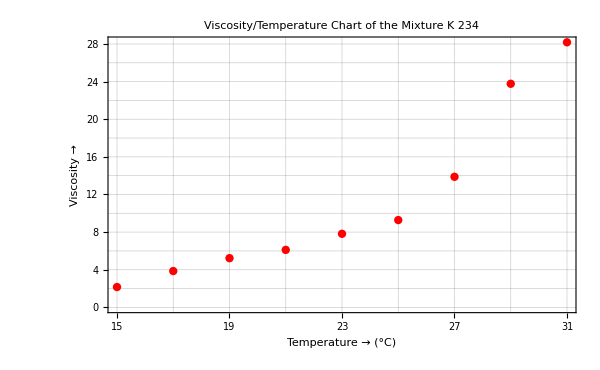

```mathematica
ListPlot[experienceSet ,
Frame-> {{True,None},{True, None}},
FrameStyle->{{Directive[Thick,Orange],None},{{Thick,Blue},None}},
FrameLabel->{{Style["Viscosity → \n",Orange, FontFamily-> "Segoe UI", FontSize->22],None},{Style["\nTemperature →  (°C) ",Blue, FontFamily-> "Segoe UI", FontSize->22],None}},
ImageSize->600,
PlotStyle->{Red,PointSize[0.01]},
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"],
FrameTicks->{{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30},None},{{15,17,19,21,23,25,27,29,31,33},None}},
GridLines->{{15,17,19,21,23,25,27,29,31},{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30}}
]
```

Also grid colors,

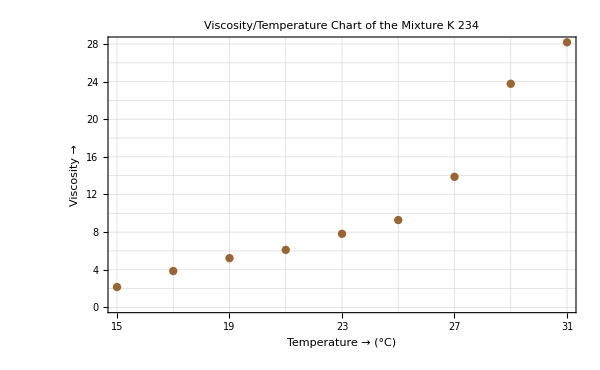

```mathematica
ListPlot[experienceSet ,
Frame-> {{True,None},{True, None}},
FrameStyle->{{Directive[Thick,Orange],None},{{Thick,Blue},None}},
FrameLabel->{{Style["Viscosity → \n",Orange, FontFamily-> "Segoe UI", FontSize->22],None},{Style["\nTemperature →  (°C) ",Blue, FontFamily-> "Segoe UI", FontSize->22],None}},
ImageSize->600,
PlotStyle->{Brown,PointSize[0.01]},
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"],
FrameTicks->{{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30},None},{{15,17,19,21,23,25,27,29,31,33},None}},
GridLines->{{15,17,19,21,23,25,27,29,31},{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30}},
GridLinesStyle->{
{Directive[Blue,Dashed]},
{Directive[Orange,Dashed]}
}
]
```

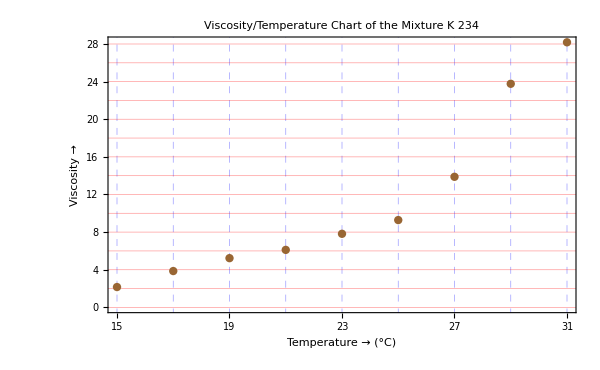

```mathematica
ListPlot[experienceSet ,
Frame-> {{True,None},{True, None}},
FrameStyle->{{Directive[Thick,Orange],None},{{Thick,Blue},None}},
FrameLabel->{{Style["Viscosity → \n",Orange, FontFamily-> "Segoe UI", FontSize->22],None},{Style["\nTemperature →  (°C) ",Blue, FontFamily-> "Segoe UI", FontSize->22],None}},
ImageSize->600,
PlotStyle->{Brown,PointSize[0.01]},
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"],
FrameTicks->{{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30},None},{{15,17,19,21,23,25,27,29,31,33},None}},

GridLines->{{{15,Directive[Blue,Dashed]},{17,Directive[Blue,Dashed]},{19,Directive[Blue,Dashed]},{21,Directive[Blue,Dashed]},{23,Directive[Blue,Dashed]},{25,Directive[Blue,Dashed]},{27,Directive[Blue,Dashed]},{29,Directive[Blue,Dashed]},{31,Directive[Blue,Dashed]}},{{0,Red},{2,Red},{4,Red},{6,Red},{8,Red},{10,Red},{12,Red},{14,Red},{16,Red},{18,Red},{20,Red},{22,Red},{24,Red},{26,Red},{28,Red},{30,Red}}}
]
```

In  Mathematica there is more than a one way to achieve things. But for even publication quality, these examples may suit some needs. All the graphs is customisable for any data and any choice. Mathematica has many other tweaks for plottting anything, these examples are the simplest show-up for scatter plots.

If we want everything in black and white, the plot definition is lot simpler.

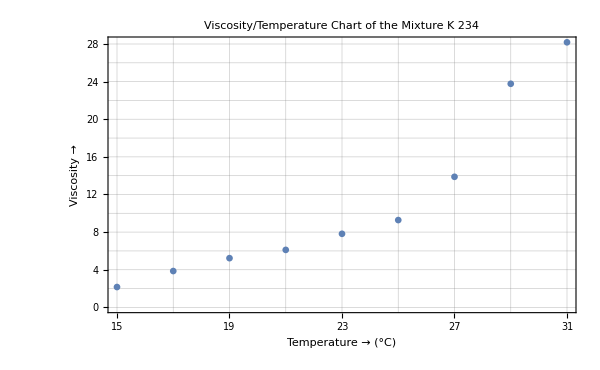

```mathematica
ListPlot[experienceSet ,
Frame-> {{True,None},{True, None}},
FrameLabel->{{Style["Viscosity → \n", FontFamily-> "Segoe UI", FontSize->22],None},{Style["\nTemperature →  (°C) ", FontFamily-> "Segoe UI", FontSize->22],None}},
ImageSize->600,
PlotStyle->{PointSize[0.008]},
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"],
FrameTicks->{{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30},None},{{15,17,19,21,23,25,27,29,31,33},None}},
GridLines-> {{15,17,19,21,23,25,27,29,31,33},{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30}}]
```

When frames are closed, we can have more presentable plots.

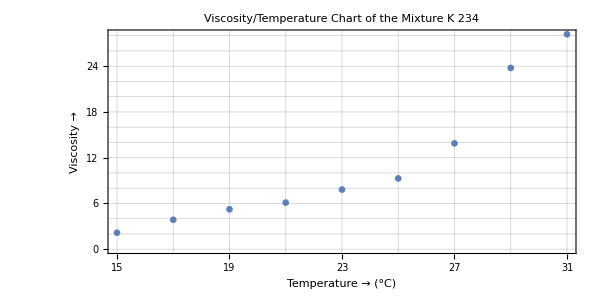

```mathematica
ListPlot[experienceSet ,
AspectRatio->0.5,
Frame-> {{True,True},{True, True}},
FrameLabel->{{Style["Viscosity → \n", FontFamily-> "Segoe UI", FontSize->22],None},{Style["\nTemperature →  (°C) ", FontFamily-> "Segoe UI", FontSize->22],None}},
ImageSize->600,
PlotStyle->{PointSize[0.008]},
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"],
FrameTicks->{{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30},None},{{15,17,19,21,23,25,27,29,31,33},None}},
GridLines-> {{15,17,19,21,23,25,27,29,31,33},{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30}}]
```

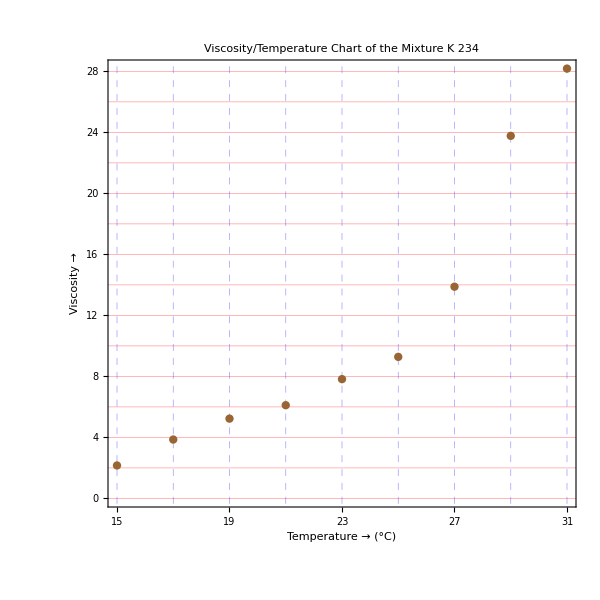

```mathematica
ListPlot[experienceSet ,
AspectRatio->1,
Frame-> {{True,True},{True, True}},
FrameStyle->{{Directive[Thick,Orange],None},{{Thick,Blue},None}},
FrameLabel->{{Style["Viscosity → \n",Orange, FontFamily-> "Segoe UI", FontSize->22],None},{Style["\nTemperature →  (°C) ",Blue, FontFamily-> "Segoe UI", FontSize->22],None}},
ImageSize->600,
PlotStyle->{Brown,PointSize[0.01]},
PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"],
FrameTicks->{{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30},None},{{15,17,19,21,23,25,27,29,31,33},None}},

GridLines->{{{15,Directive[Blue,Dashed]},{17,Directive[Blue,Dashed]},{19,Directive[Blue,Dashed]},{21,Directive[Blue,Dashed]},{23,Directive[Blue,Dashed]},{25,Directive[Blue,Dashed]},{27,Directive[Blue,Dashed]},{29,Directive[Blue,Dashed]},{31,Directive[Blue,Dashed]}},{{0,Red},{2,Red},{4,Red},{6,Red},{8,Red},{10,Red},{12,Red},{14,Red},{16,Red},{18,Red},{20,Red},{22,Red},{24,Red},{26,Red},{28,Red},{30,Red}}}
]
```

Grids may be defined with a simpler way, if all x grids and y grids have their own block colors and style.

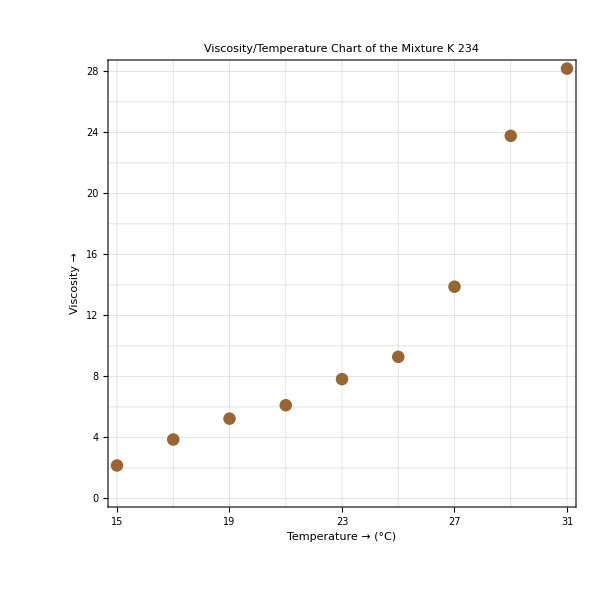

```mathematica
ListPlot[experienceSet ,

AspectRatio->1,

Frame-> {{True,True},{True, True}},

FrameStyle->{{Directive[Thick,Orange],None},{{Thick,Blue},None}},

FrameLabel->{{Style["Viscosity → \n",Orange, FontFamily-> "Segoe UI", FontSize->22],None},{Style["\nTemperature →  (°C) ",Blue, FontFamily-> "Segoe UI", FontSize->22],None}},
ImageSize->600,

PlotStyle->{Brown,PointSize[0.015]},

PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"],

FrameTicks->{
{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30},None},{{15,17,19,21,23,25,27,29,31,33},None}
},

GridLines->{
{15,17,19,21,23,25,27,29,31},
{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30}
},

GridLinesStyle->{
{Directive[Red,Dashed]},{Directive[Blue,Dashed]}
}
]
```

Adding some text with Epilog [ ].

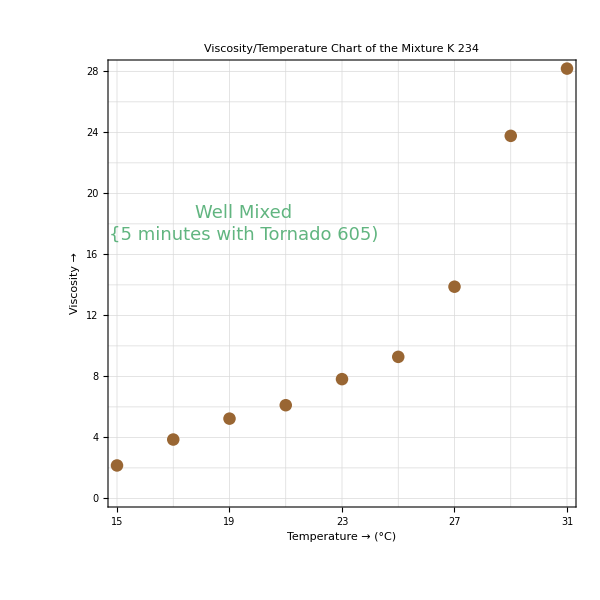

```mathematica
ListPlot[experienceSet ,

AspectRatio->1,

Frame-> {{True,True},{True, True}},

FrameStyle->{{Directive[Thick,Orange],None},{{Thick,Blue},None}},

FrameLabel->{{Style["Viscosity → \n",Orange, FontFamily-> "Segoe UI", FontSize->22],None},{Style["\nTemperature →  (°C) ",Blue, FontFamily-> "Segoe UI", FontSize->22],None}},
ImageSize->600,

PlotStyle->{Brown,PointSize[0.015]},

PlotLabel->Style["Viscosity/Temperature Chart of the Mixture K 234\n",24, Red,FontFamily->"Segoe UI"],

FrameTicks->{
{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30},None},{{15,17,19,21,23,25,27,29,31,33},None}
},

GridLines->{
{15,17,19,21,23,25,27,29,31},
{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30}
},

GridLinesStyle->{
{Directive[Red,Dashed]},{Directive[Blue,Dashed]}
},

Epilog->{
Text
[
Style[
"Well Mixed\n{5 minutes with Tornado 605)",
FontFamily->"Segoe UI",
FontSize->18,
RGBColor[0.38,0.71,0.5]
],
{19.5,18},{0,0},{1,0}
]
}
]
```

Have good time when applying them...